```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichiro/Documents/Univ/SLattice/peak_theory

```mathematica
ALIZARIN=RGBColor["#e74c3c"]
PETERRIVER=RGBColor["#3498db"]
```

RGBColor[0.9058823529411765, 0.2980392156862745, 0.23529411764705882]

RGBColor[0.20392156862745098, 0.596078431372549, 0.8588235294117647]

## Direct Sampling

```mathematica
npeak=16;
NL=256;
kpeak=2π npeak/NL;
```

### LN σ^2=0.01

```mathematica
s2s=1/100;
s2string="0,01";
As=5 10^-3;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1,s2->s2s};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2,s2->s2s};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3,s2->s2s};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4,s2->s2s};
```

```mathematica
CprofDS=Join@@Table[Import["data/paper/LN_"<>s2string<>"/LN_Cprof_"<>s2string<>"_256_16_"<>ToString[i]<>".csv"],{i,0,99}];
nuP=CprofDS[[All,4]]/σ2;
k3P=CprofDS[[All,5]]Sqrt[σ2/σ4];
nuk3P=CprofDS[[All,4;;5]].DiagonalMatrix[{1/σ2,Sqrt[σ2/σ4]}];
```

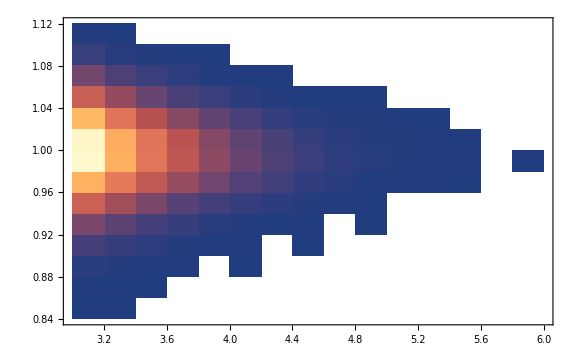

```mathematica
DensityHistogram[nuk3P]
```

```mathematica
numin=4;
numax=4.5;
nucenter=(numin+numax)/2
k3center=Mean[k3P]
k3min=k3center-0.05;
k3max=k3center+0.05;
```

4.25

0.998233

```mathematica
bs=Select[Range[Length[CprofDS]],numin<=nuP[[#]]<numax&&k3min<=k3P[[#]]<k3max&];bs//Length
zlatN=CprofDS[[bs,22;;34]];
```

2297

```mathematica
WRTH[z_]=3(Sin[z]-z Cos[z])/z^3;
```

```mathematica
calPz[lnk_,s2_]=Ag/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
ψn[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]Sinc[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n+1) lnk)calPz[lnk,s2]Sinc'[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψn[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψn[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψnp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψnp[x,2,s2s]},{x,10^-2,10,10^-2}];
]
```

{18.4157,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζt[x_,nu2_,k3t_]=Sqrt[σn2[0,s2s]](γn[s2s]nu2)/(1-γn[s2s]^2)((1-γn[s2s] k3t^2)ψ1int[x]+γn[s2s]^3(k3t^2-γn[s2s])ψ2int[x])/.{Ag->As};
ζtp[x_,nu2_,k3t_]=Sqrt[σn2[0,s2s]](γn[s2s]nu2)/(1-γn[s2s]^2)((1-γn[s2s] k3t^2)ψ1pint[x]+γn[s2s]^3(k3t^2-γn[s2s])ψ2pint[x])/.{Ag->As};
```

```mathematica
Deltaζ[x_]=Sqrt[σn2[0,s2s](1-γn[s2s]^2/(1-γn[s2s]^2)(ψ1int[x]^2-2 γn[s2s]^4 ψ1int[x]ψ2int[x]+γn[s2s]^6 ψ2int[x]^2))/.{Ag->As}];
```

```mathematica
Table[i,{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}]//Length
```

40

```mathematica
padding={{100,10},{70,20}};
```

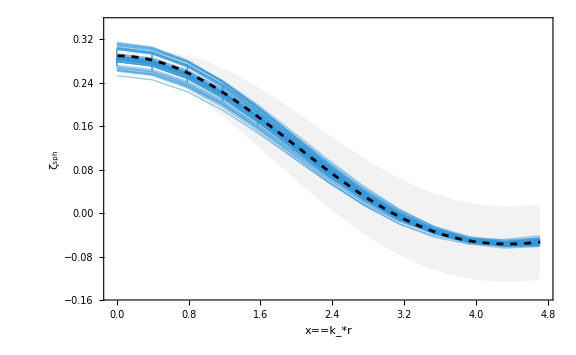

```mathematica
Show[Plot[{ζt[x,nucenter,k3center]+Deltaζ[x],ζt[x,nucenter,k3center]-Deltaζ[x]},{x,0.01,kpeak 12},PlotRange->{{-0.05,kpeak 12+0.05},{-0.15,0.35}},Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[Gray,Opacity[0.1]],FrameLabel->{x=="k_*r",Subscript[ζ, "sph"]},ImagePadding->padding],
ListPlot[Table[Transpose[{kpeak Range[0,12],zlatN[[i]]}],{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}],PlotStyle->Directive[PETERRIVER,Thin,Opacity[0.5]]],
ListPlot[Transpose[{kpeak Range[0,12],Around@@@Transpose[{Mean[zlatN],StandardDeviation/@Transpose[zlatN]}]}],PlotStyle->{{AbsoluteThickness[3],PETERRIVER}}],
Plot[ζt[x,nucenter,k3center],{x,0.01,kpeak 12},PlotStyle->{Black,Dashed}]]
```

```mathematica
ClatN=CprofDS[[bs,10;;21]];
```

```mathematica
δt[x_,nu2_,k3t_]=-4/3 x ζtp[x,nu2,k3t];
calCt[x_,nu2_,k3t_]=δt[x,nu2,k3t]-3/8 δt[x,nu2,k3t]^2;
```

```mathematica
ψnr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]WRTH[E^lnk x]//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnrr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2] WRTH[E^lnk x]^2//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[ψ2rList=ParallelTable[{x,ψnr[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ3rList=ParallelTable[{x,ψnr[x,3,s2s]},{x,10^-2,10,10^-2}];
ψ2rrList=ParallelTable[{x,ψnrr[x,2,s2s]},{x,10^-2,10,10^-2}];]
```

{25.1071,Null}

```mathematica
ψ2rint[x_]=Interpolation[ψ2rList][x];
ψ3rint[x_]=Interpolation[ψ3rList][x];
ψ2rrint[x_]=Interpolation[ψ2rrList][x];
```

```mathematica
Varδ[x_]=16/81 σn2[0,s2s](σn2[2,s2s]/σn2[0,s2s] x^4/ks^4 ψ2rrint[x]-γn[s2s]^2/(1-γn[s2s]^2)(σn2[2,s2s]^2/σn2[1,s2s]^2 x^4/ks^4 ψ2rint[x]^2-2 γn[s2s]^4 σn2[3,s2s]/σn2[1,s2s] x^4/ks^4 ψ2rint[x]ψ3rint[x]+γn[s2s]^6 σn2[3,s2s]^2/σn2[2,s2s]^2 x^4/ks^4 ψ3rint[x]^2))/.{Ag->As};
```

```mathematica
ΔC[x_,nu2_,k3t_]=Sqrt[((1-3/4 δt[x,nu2,k3t])^2+9/32 Varδ[x])Varδ[x]];
```

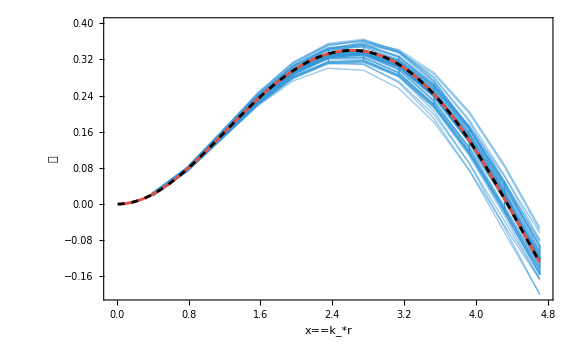

```mathematica
Show[Plot[{calCt[x,nucenter,k3center]-3/8 Varδ[x]+ΔC[x,nucenter,k3center],calCt[x,nucenter,k3center]-3/8 Varδ[x]-ΔC[x,nucenter,k3center]},{x,0.01,kpeak 12},Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[Gray,Opacity[0.1]],FrameLabel->{x=="k_*r",𝒞},PlotRange->{{-0.05,kpeak 12+0.05},{-0.2,0.4}},ImagePadding->padding],
ListPlot[Table[Transpose[{kpeak Range[1,12],ClatN[[i]]}],{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}],PlotStyle->Directive[PETERRIVER,Thin,Opacity[0.5]]],
ListPlot[Transpose[{kpeak Range[1,12],Around@@@Transpose[{Mean[ClatN],StandardDeviation/@Transpose[ClatN]}]}],PlotStyle->{{AbsoluteThickness[3],PETERRIVER}}],
Plot[{calCt[x,nucenter,k3center],calCt[x,nucenter,k3center]-3/8 Varδ[x]},{x,0.01,kpeak 12},PlotStyle->{ALIZARIN,{Black,Dashed}}]]
```

### LN σ^2=0.1

```mathematica
s2s=1/10;
s2string="0,1";
As=5 10^-3;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1,s2->s2s};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2,s2->s2s};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3,s2->s2s};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4,s2->s2s};
```

```mathematica
CprofDS=Join@@Table[Import["data/paper/LN_"<>s2string<>"/LN_Cprof_"<>s2string<>"_256_16_"<>ToString[i]<>".csv"],{i,0,99}];
nuP=CprofDS[[All,4]]/σ2;
k3P=CprofDS[[All,5]]Sqrt[σ2/σ4];
nuk3P=CprofDS[[All,4;;5]].DiagonalMatrix[{1/σ2,Sqrt[σ2/σ4]}];
```

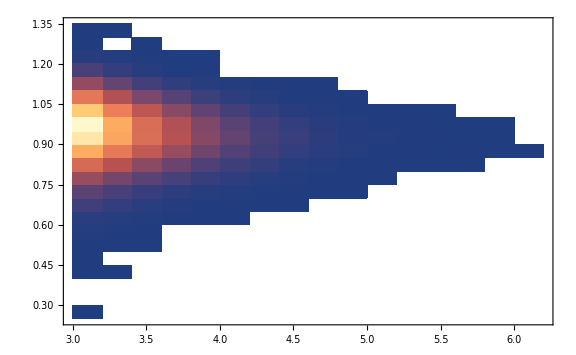

```mathematica
DensityHistogram[nuk3P]
```

```mathematica
numin=4;
numax=4.5;
nucenter=(numin+numax)/2
k3center=Mean[k3P]
k3min=k3center-0.05;
k3max=k3center+0.05;
```

4.25

0.944399

```mathematica
bs=Select[Range[Length[CprofDS]],numin<=nuP[[#]]<numax&&k3min<=k3P[[#]]<k3max&];bs//Length
zlatN=CprofDS[[bs,22;;34]];
```

3261

```mathematica
WRTH[z_]=3(Sin[z]-z Cos[z])/z^3;
```

```mathematica
calPz[lnk_,s2_]=Ag/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
ψn[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]Sinc[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n+1) lnk)calPz[lnk,s2]Sinc'[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψn[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψn[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψnp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψnp[x,2,s2s]},{x,10^-2,10,10^-2}];
]
```

{35.1976,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
ζt[x_,nu2_,k3t_]=Sqrt[σn2[0,s2s]](γn[s2s]nu2)/(1-γn[s2s]^2)((1-γn[s2s] k3t^2)ψ1int[x]+γn[s2s]^3(k3t^2-γn[s2s])ψ2int[x])/.{Ag->As};
ζtp[x_,nu2_,k3t_]=Sqrt[σn2[0,s2s]](γn[s2s]nu2)/(1-γn[s2s]^2)((1-γn[s2s] k3t^2)ψ1pint[x]+γn[s2s]^3(k3t^2-γn[s2s])ψ2pint[x])/.{Ag->As};
```

```mathematica
Deltaζ[x_]=Sqrt[σn2[0,s2s](1-γn[s2s]^2/(1-γn[s2s]^2)(ψ1int[x]^2-2 γn[s2s]^4 ψ1int[x]ψ2int[x]+γn[s2s]^6 ψ2int[x]^2))/.{Ag->As}];
```

```mathematica
Table[i,{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}]//Length
```

40

```mathematica
padding={{100,10},{70,20}};
```

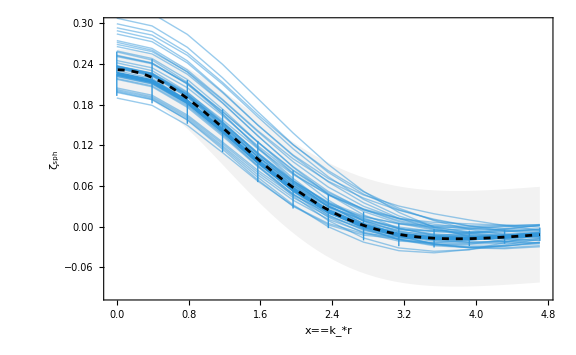

```mathematica
Show[Plot[{ζt[x,nucenter,k3center]+Deltaζ[x],ζt[x,nucenter,k3center]-Deltaζ[x]},{x,0.01,kpeak 12},PlotRange->{{-0.05,kpeak 12+0.05},{-0.1,0.3}},Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[Gray,Opacity[0.1]],FrameLabel->{x=="k_*r",Subscript[ζ, "sph"]},ImagePadding->padding],
ListPlot[Table[Transpose[{kpeak Range[0,12],zlatN[[i]]}],{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}],PlotStyle->Directive[PETERRIVER,Thin,Opacity[0.5]]],
ListPlot[Transpose[{kpeak Range[0,12],Around@@@Transpose[{Mean[zlatN],StandardDeviation/@Transpose[zlatN]}]}],PlotStyle->{{AbsoluteThickness[3],PETERRIVER}}],
Plot[ζt[x,nucenter,k3center],{x,0.01,kpeak 12},PlotStyle->{Black,Dashed}]]
```

```mathematica
ClatN=CprofDS[[bs,10;;21]];
```

```mathematica
δt[x_,nu2_,k3t_]=-4/3 x ζtp[x,nu2,k3t];
calCt[x_,nu2_,k3t_]=δt[x,nu2,k3t]-3/8 δt[x,nu2,k3t]^2;
```

```mathematica
ψnr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]WRTH[E^lnk x]//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnrr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2] WRTH[E^lnk x]^2//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[ψ2rList=ParallelTable[{x,ψnr[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ3rList=ParallelTable[{x,ψnr[x,3,s2s]},{x,10^-2,10,10^-2}];
ψ2rrList=ParallelTable[{x,ψnrr[x,2,s2s]},{x,10^-2,10,10^-2}];]
```

{41.0541,Null}

```mathematica
ψ2rint[x_]=Interpolation[ψ2rList][x];
ψ3rint[x_]=Interpolation[ψ3rList][x];
ψ2rrint[x_]=Interpolation[ψ2rrList][x];
```

```mathematica
Varδ[x_]=16/81 σn2[0,s2s](σn2[2,s2s]/σn2[0,s2s] x^4/ks^4 ψ2rrint[x]-γn[s2s]^2/(1-γn[s2s]^2)(σn2[2,s2s]^2/σn2[1,s2s]^2 x^4/ks^4 ψ2rint[x]^2-2 γn[s2s]^4 σn2[3,s2s]/σn2[1,s2s] x^4/ks^4 ψ2rint[x]ψ3rint[x]+γn[s2s]^6 σn2[3,s2s]^2/σn2[2,s2s]^2 x^4/ks^4 ψ3rint[x]^2))/.{Ag->As};
```

```mathematica
ΔC[x_,nu2_,k3t_]=Sqrt[((1-3/4 δt[x,nu2,k3t])^2+9/32 Varδ[x])Varδ[x]];
```

```mathematica
Sqrt[γn[s2s]]//N
```

0.904837

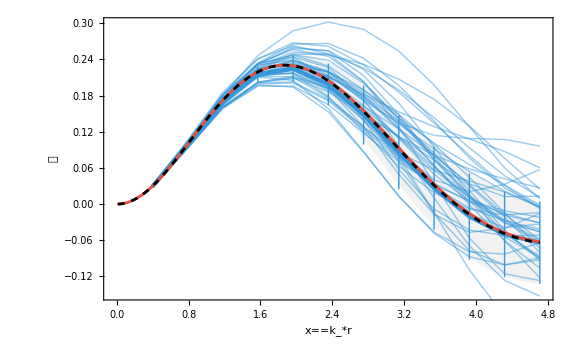

```mathematica
Show[Plot[{calCt[x,nucenter,k3center]-3/8 Varδ[x]+ΔC[x,nucenter,k3center],calCt[x,nucenter,k3center]-3/8 Varδ[x]-ΔC[x,nucenter,k3center]},{x,0.01,kpeak 12},Filling->{1->{2}},PlotStyle->None,FillingStyle->Directive[Gray,Opacity[0.1]],FrameLabel->{x=="k_*r",𝒞},PlotRange->{{-0.05,kpeak 12+0.05},{-0.15,0.3}},ImagePadding->padding],
ListPlot[Table[Transpose[{kpeak Range[1,12],ClatN[[i]]}],{i,1,Length[bs],Max[1,Floor[Length[bs]/39]]}],PlotStyle->Directive[PETERRIVER,Thin,Opacity[0.5]]],
ListPlot[Transpose[{kpeak Range[1,12],Around@@@Transpose[{Mean[ClatN],StandardDeviation/@Transpose[ClatN]}]}],PlotStyle->{{AbsoluteThickness[3],PETERRIVER}}],
Plot[{calCt[x,nucenter,k3center],calCt[x,nucenter,k3center]-3/8 Varδ[x]},{x,0.01,kpeak 12},PlotStyle->{ALIZARIN,{Black,Dashed}}]]
```